```mathematica
SetDirectory["/home/uyras/projects/partsEngine/build-PartsEngine-Desktop_Qt_5_4_0_GCC_64bit-Debug"];
```

```mathematica
(*Сохраняет в TIFF формате график посещенных энергий для каждого потока*)
energies = Union[ReadList["energies.txt"]];
ParallelTable[
Export["oe_"<>ToString[i]<>".tif",
data=ReadList["e_"<>ToString[i]<>".txt"];
dataLen=Length[data];
plot=Join[{data},Table[{{0,i},{dataLen,i}},{i,energies}]];
ListLinePlot[plot]
,"TIFF",ImageSize->1920
];,{i,0,49}
];
```

$Aborted

1.86319

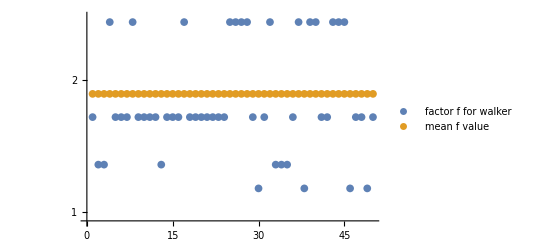

0 | 1.64872
1 | 1.28403
2 | 1.28403
3 | 2.71828
4 | 1.64872
5 | 1.64872
6 | 1.64872
7 | 2.71828
8 | 1.64872
9 | 1.64872
10 | 1.64872
11 | 1.64872
12 | 1.28403
13 | 1.64872
14 | 1.64872
15 | 1.64872
16 | 2.71828
17 | 1.64872
18 | 1.64872
19 | 1.64872
20 | 1.64872
21 | 1.64872
22 | 1.64872
23 | 1.64872
24 | 2.71828
25 | 2.71828
26 | 2.71828
27 | 2.71828
28 | 1.64872
29 | 1.13315
30 | 1.64872
31 | 2.71828
32 | 1.28403
33 | 1.28403
34 | 1.28403
35 | 1.64872
36 | 2.71828
37 | 1.13315
38 | 2.71828
39 | 2.71828
40 | 1.64872
41 | 1.64872
42 | 2.71828
43 | 2.71828
44 | 2.71828
45 | 1.13315
46 | 1.64872
47 | 1.64872
48 | 1.13315
49 | 1.64872

```mathematica
(* Выборка всех модификационных факторов из аналитики процесса*)
desc = OpenRead["analys.txt"];
Skip[desc,String];
data=Last/@ReadList[desc,Number,RecordLists->True];
mean = Mean[data](*Средний модификационный фактор*)
ListLogPlot[{data,Table[mean,{i,Length[data]}]},PlotRange->{0.95,2.8},PlotLegends->{"factor f for walker","mean f value"}]
Grid[Table[{i-1,data[[i]]},{i,1,Length[data]}],Frame->All]
```